```mathematica
-Graphics--Graphics--Graphics-                                                              -Graphics-
```

```mathematica
z=d*(e+ⅈ*(1-e)*(Cos[kx*a] -Cos[ky*a]))
```

d (e+ⅈ (1-e) (Cos[a kx]-Cos[a ky]))

```mathematica
abs=ComplexExpand[Abs[z]]
arg=ComplexExpand[Arg[z],TargetFunctions->{Re,Im}]
```

√(d^2) √(e^2+(1-e)^2 (Cos[a kx]-Cos[a ky])^2)

ArcTan[d e,d (1-e) (Cos[a kx]-Cos[a ky])]

```mathematica
abss[d_,e_,a_]:=d*(Cos[a kx]-Cos[a ky])^1
```

```mathematica
absd[d_,e_,a_]:=√(d^2) √(e^2+(1-e)^2 (Cos[a kx]-Cos[a ky])^2)
```

```mathematica
DensityPlot[absd[1,0.5,1], {kx,-2*π,2*π},{ky,-2*π,2*π}]
```

```mathematica
absd[th_,d_,a_]:=d*(Cos[a Cos[th]]-Cos[a Sin[th]])
```

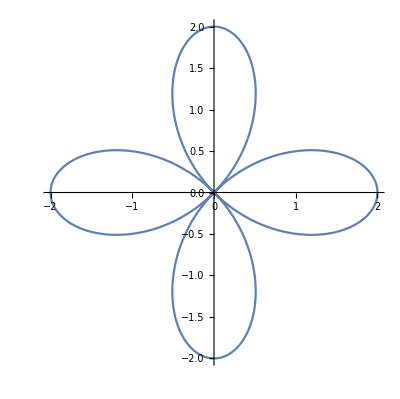

```mathematica
PolarPlot[absd[th,1,π],{th,0,2*π}]
```

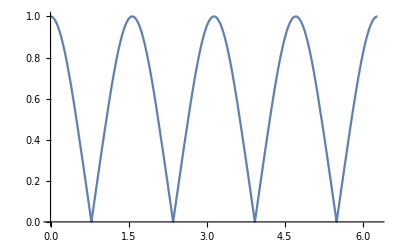

```mathematica
Plot[{Abs[absd[th,0.5,π]]},{th,0,2*π}]
```

```mathematica
ag=ComplexExpand[Arg[d*(Cos[a Cos[th]]-Cos[a Sin[th]])]]
```

Arg[d (Cos[a Cos[th]]-Cos[a Sin[th]])]

```mathematica
argd[th_,d_,a_]:=ArcTan[d (Cos[a Cos[th]]-Cos[a Sin[th]])]
```

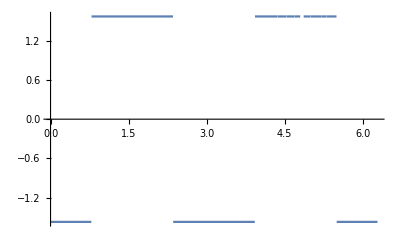

```mathematica
Plot[{ArcSin[absd[th,0.5,π]/Abs[absd[th,0.5,π]]]},{th,0,2*π}]
```

```mathematica
spid[d_,e_,th_,a_]:=d*(e+ⅈ*(1-e)*(Cos[Cos[th]*a] -Cos[Sin[th]*a]))
```

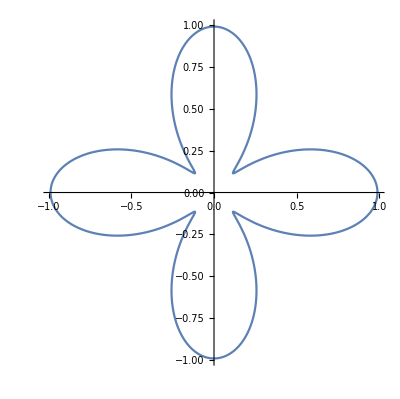

```mathematica
PolarPlot[Abs[spid[.65,0.25,th,π]],{th,0,2*π}]
```

```mathematica
DPID=Animate[PolarPlot[Abs[spid[1,e,th,π]],{th,0,2*π}],{e,0,1},AnimationRunning->False]
```

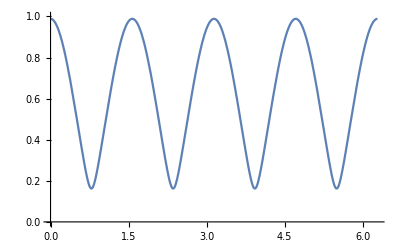

```mathematica
Plot[{Abs[spid[.65,0.25,th,π]]},{th,0,2*π},PlotRange->{0,1}]
```

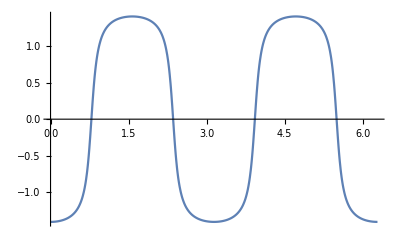

```mathematica
Plot[{ArcSin[Im[spid[.65,0.25,th,π]]/Abs[spid[.65,0.25,th,π]]]},{th,0,2*π}]
```

```mathematica
dpid[d_,e_,th_,a_]:=d*((1-e)*(Cos[Cos[th]*a]-Cos[Sin[th]*a])+ⅈ*e*2*Sin[Cos[th]*a]*Sin[Sin[th]*a])
```

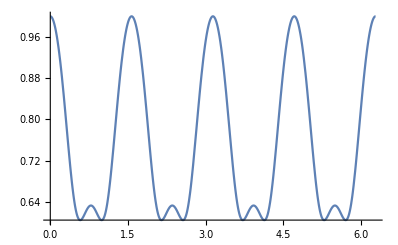

```mathematica
Plot[Abs[dpid[1,0.5,th,π]],{th,0,2*π}]
```

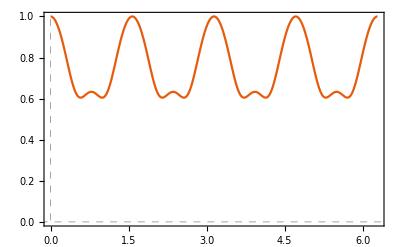

```mathematica
Plot[Abs[dpid[1,0.5,th,π]],{th,0,2 π},PlotTheme->"Scientific",GridLinesStyle->Directive[Gray, Dashed],PlotRange->{0,1}]
```

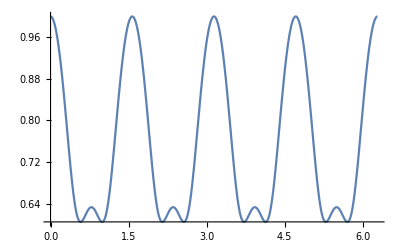

```mathematica
Show[%28,PlotLabel->None,LabelStyle->{13,GrayLevel[0]}]
```

```mathematica
Plot[Abs[dpid[1,0.5,th,π]],{th,0,2 π},PlotTheme->"Detailed"]
```

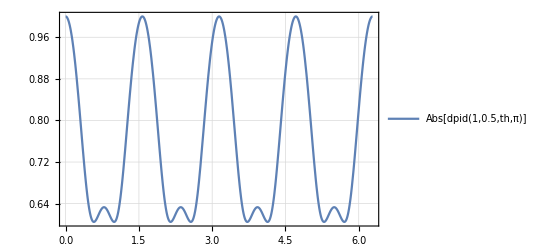

```mathematica
DPID=Animate[PolarPlot[Abs[dpid[1,e,th,π]],{th,0,2*π}],{e,0,1},AnimationRunning->False]
```

```mathematica
Export["DPID.avi",DPID]
```

DPID.avi

```mathematica
PlotLegend->{"0","0.2","0.4","0.5","0.6","0.8","1.0"}
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["DPID.avi"]]]
```

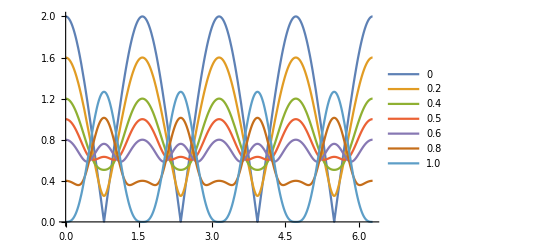

```mathematica
Plot[{Abs[dpid[1,0.0,th,π]],Abs[dpid[1,0.2,th,π]],Abs[dpid[1,0.4,th,π]],Abs[dpid[1,0.5,th,π]],Abs[dpid[1,0.6,th,π]],Abs[dpid[1,0.8,th,π]],Abs[dpid[1,1,th,π]]},{th,0,2*π},PlotLegends->{"0","0.2","0.4","0.5","0.6","0.8","1.0"},LabelStyle->{13,GrayLevel[0]}]
```

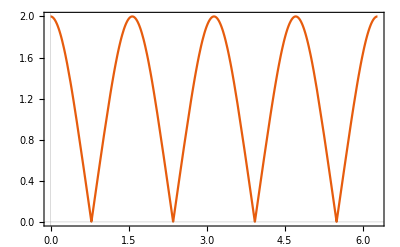

```mathematica
Plot[Abs[dpid[1,0.0,th,π]],{th,0,2*π},LabelStyle->{14,GrayLevel[0]},PlotTheme->"Scientific"]
```

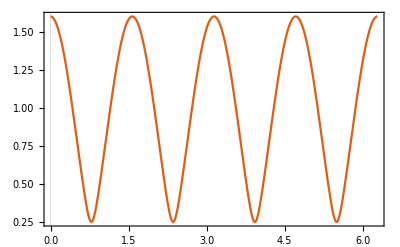

```mathematica
Plot[Abs[dpid[1,0.2,th,π]],{th,0,2*π},LabelStyle->{14,GrayLevel[0]},PlotTheme->"Scientific"]
```

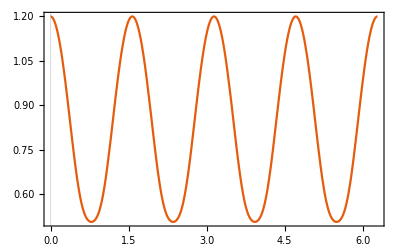

```mathematica
Plot[Abs[dpid[1,0.4,th,π]],{th,0,2*π},LabelStyle->{14,GrayLevel[0]},PlotTheme->"Scientific"]
```

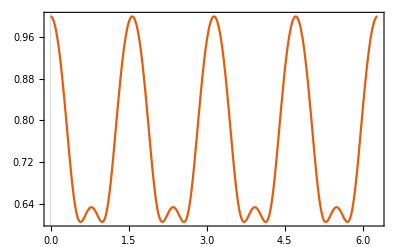

```mathematica
Plot[Abs[dpid[1,0.5,th,π]],{th,0,2*π},LabelStyle->{14,GrayLevel[0]},PlotTheme->"Scientific"]
```

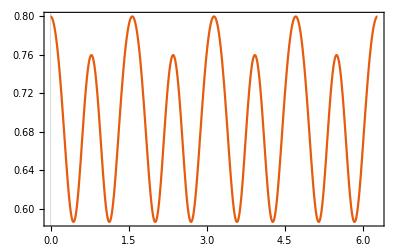

```mathematica
Plot[Abs[dpid[1,0.6,th,π]],{th,0,2*π},LabelStyle->{14,GrayLevel[0]},PlotTheme->"Scientific"]
```

```mathematica
Plot[Abs[dpid[1,0.6,th,π]],{th,0,2*π},LabelStyle->{14,GrayLevel[0]},PlotTheme->"Scientific"]
```

-Graphics-

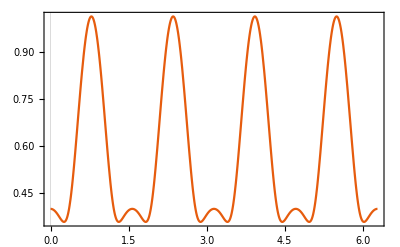

```mathematica
Plot[Abs[dpid[1,0.8,th,π]],{th,0,2*π},LabelStyle->{14,GrayLevel[0]},PlotTheme->"Scientific"]
```

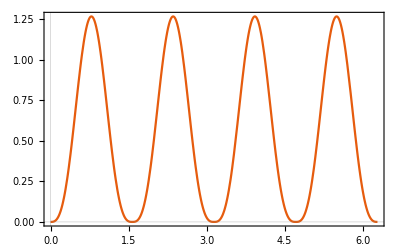

```mathematica
Plot[Abs[dpid[1,1.0,th,π]],{th,0,2*π},LabelStyle->{14,GrayLevel[0]},PlotTheme->"Scientific"]
```

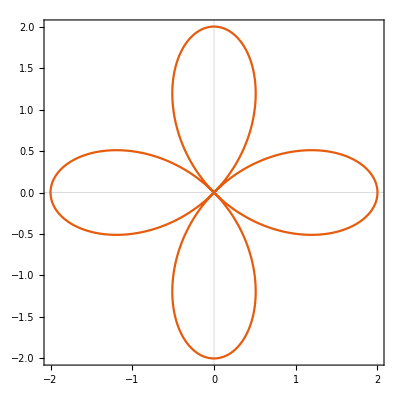

```mathematica
PolarPlot[Abs[dpid[1,0,th,π]],{th,0,2*π},LabelStyle->{14,GrayLevel[0]},PlotTheme->"Scientific"]
```

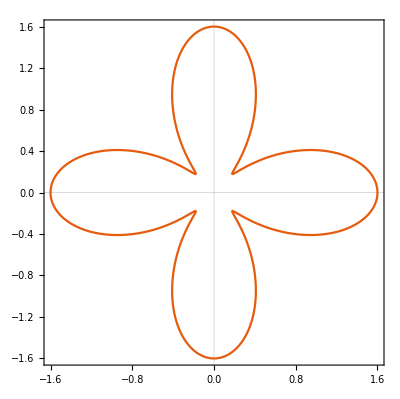

```mathematica
PolarPlot[Abs[dpid[1,0.2,th,π]],{th,0,2*π},LabelStyle->{14,GrayLevel[0]},PlotTheme->"Scientific"]
```

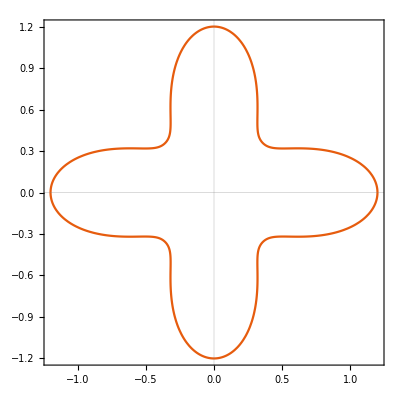

```mathematica
PolarPlot[Abs[dpid[1,0.4,th,π]],{th,0,2*π},LabelStyle->{14,GrayLevel[0]},PlotTheme->"Scientific"]
```

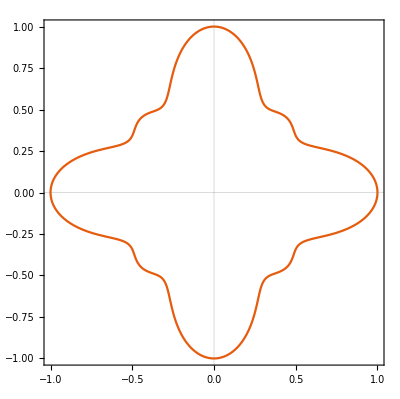

```mathematica
PolarPlot[Abs[dpid[1,0.5,th,π]],{th,0,2*π},LabelStyle->{14,GrayLevel[0]},PlotTheme->"Scientific"]
```

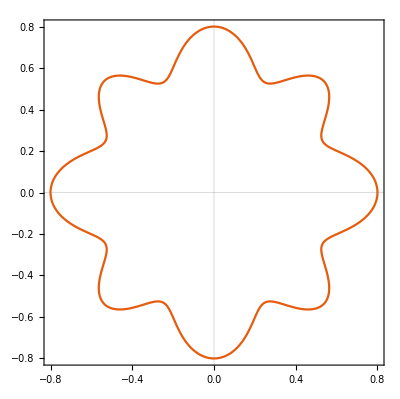

```mathematica
PolarPlot[Abs[dpid[1,0.6,th,π]],{th,0,2*π},LabelStyle->{14,GrayLevel[0]},PlotTheme->"Scientific"]
```

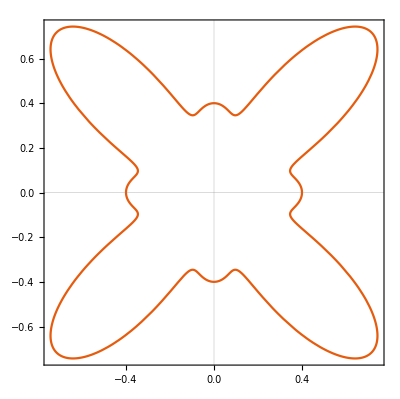

```mathematica
PolarPlot[Abs[dpid[1,0.8,th,π]],{th,0,2*π},LabelStyle->{14,GrayLevel[0]},PlotTheme->"Scientific"]
```

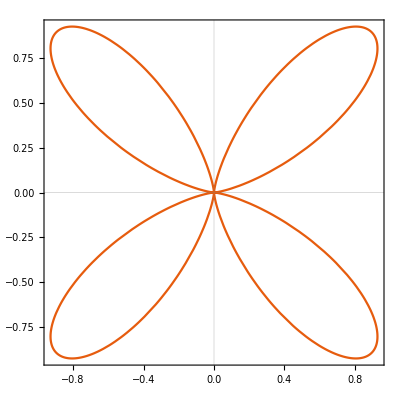

```mathematica
PolarPlot[Abs[dpid[1,1,th,π]],{th,0,2*π},LabelStyle->{14,GrayLevel[0]},PlotTheme->"Scientific"]
```